```mathematica
(*Matrix of eigenvectors, parametrized by (θp,ϕp) in (S^2)_+, and (θm,ϕm) in (S^2)_-
(see Appendix C of "Geometric approach to fragile topology beyond symmetry indicators"). *)
R4D={{Cos[θm/2] Cos[ϕp/2] Cos[(θp+ϕm)/2]-Sin[θm/2] Sin[ϕp/2] Sin[(θp-ϕm)/2],Cos[θm/2] Cos[(θp-ϕm)/2] Sin[ϕp/2]-Cos[ϕp/2] Sin[θm/2] Sin[(θp+ϕm)/2],-Cos[(θp-ϕm)/2] Sin[θm/2] Sin[ϕp/2]-Cos[θm/2] Cos[ϕp/2] Sin[(θp+ϕm)/2],Cos[ϕp/2] Cos[(θp+ϕm)/2] Sin[θm/2]+Cos[θm/2] Sin[ϕp/2] Sin[(θp-ϕm)/2]},{-Cos[θm/2] Cos[(θp+ϕm)/2] Sin[ϕp/2]-Cos[ϕp/2] Sin[θm/2] Sin[(θp-ϕm)/2],Cos[θm/2] Cos[ϕp/2] Cos[1/2 (-θp+ϕm)]+Sin[θm/2] Sin[ϕp/2] Sin[(θp+ϕm)/2],-Cos[ϕp/2] Cos[(θp-ϕm)/2] Sin[θm/2]+Cos[θm/2] Sin[ϕp/2] Sin[(θp+ϕm)/2],-Cos[(θp+ϕm)/2] Sin[θm/2] Sin[ϕp/2]+Cos[θm/2] Cos[ϕp/2] Sin[(θp-ϕm)/2]},{-Cos[(θp-ϕm)/2] Sin[θm/2] Sin[ϕp/2]+Cos[θm/2] Cos[ϕp/2] Sin[(θp+ϕm)/2],Cos[ϕp/2] Cos[(θp+ϕm)/2] Sin[θm/2]-Cos[θm/2] Sin[ϕp/2] Sin[(θp-ϕm)/2],Cos[θm/2] Cos[ϕp/2] Cos[(θp+ϕm)/2]+Sin[θm/2] Sin[ϕp/2] Sin[(θp-ϕm)/2],Cos[θm/2] Cos[(θp-ϕm)/2] Sin[ϕp/2]+Cos[ϕp/2] Sin[θm/2] Sin[(θp+ϕm)/2]},{-Cos[ϕp/2] Cos[(θp-ϕm)/2] Sin[θm/2]-Cos[θm/2] Sin[ϕp/2] Sin[(θp+ϕm)/2],-Cos[(θp+ϕm)/2] Sin[θm/2] Sin[ϕp/2]+Cos[θm/2] Cos[ϕp/2] Sin[1/2 (-θp+ϕm)],-Cos[θm/2] Cos[(θp+ϕm)/2] Sin[ϕp/2]+Cos[ϕp/2] Sin[θm/2] Sin[(θp-ϕm)/2],Cos[θm/2] Cos[ϕp/2] Cos[1/2 (-θp+ϕm)]-Sin[θm/2] Sin[ϕp/2] Sin[(θp+ϕm)/2]}};
```

```mathematica
CHOSE A COMMON BASE POINT AT (ϕp,θp,ϕm,θm)=(0,0,π/2,π/2)
```

```mathematica
fθ=π If[Abs[ky]≤Abs[kx],Abs[kx],Abs[ky]];
fϕ=ArcTan[kx,ky];
(* (qp,pm)=the two winding numbers that fix the Euler classes to (Subscript[χ, I],Subscript[χ, II]) = (q_+-q_-,q_++q_-) *)
qp=2;-1;2;(*any integer: winding number of t_(q+) : T^2 -> (S^2)_+ *)
qm=0;2;-1;(*any integer: winding number of t_(q-) : T^2 -> (S^2)_-*)
Cp=If[qp==0,0,1];
Cm=If[qm==0,0,1];
ϵ1n=-1-0 0.4;(Cos[kx π]+Cos[ky π]);
ϵ2n=-1+0 0.4;(Cos[kx π]+Cos[ky π]);
ϵ3n=+1-0 0.4;(Cos[kx π]+Cos[ky π]);
ϵ4n=+1+0 0.4;(Cos[kx π]+Cos[ky π]);

Rm=R4D/.{ϕp->qp fϕ,θp->Cp fθ,ϕm->qm fϕ+π/2,θm->Cm fθ+π/2};
HR=Rm.DiagonalMatrix[{ϵ1n,ϵ2n,ϵ3n,ϵ4n}].Transpose[Rm];

(*Hamiltonian at Γ*)
R00=N[R4D/.{ϕp->0,θp->0,ϕm->π/2,θm->π/2}];(*{ϕp->0,θp->0,ϕm->Cm π/2,θm->Cm π/2}*)
HR00=R00.(DiagonalMatrix[{ϵ1n,ϵ2n,ϵ3n,ϵ4n}]/.{kx->0,ky->0}).Transpose[R00];
```

```mathematica
Quiet[Nk=10;20;10;50;10;20;50;50;
K1=Table[i,{i,-1.,1.,1./Nk}];
K2=Table[i,{i,-1.,1.,1./Nk}];
NK1=Dimensions[K1][[1]];
NK2=Dimensions[K2][[1]];
h11n=Table[N[HR[[1,1]]/.{kx->K1[[i]],ky->K2[[j]]}],{i,1,NK1},{j,1,NK2}];
h11n[[Nk+1,Nk+1]]=HR00[[1,1]];
h22n=Table[N[HR[[2,2]]/.{kx->K1[[i]],ky->K2[[j]]}],{i,1,NK1},{j,1,NK2}];
h22n[[Nk+1,Nk+1]]=HR00[[2,2]];
h33n=Table[N[HR[[3,3]]/.{kx->K1[[i]],ky->K2[[j]]}],{i,1,NK1},{j,1,NK2}];
h33n[[Nk+1,Nk+1]]=HR00[[3,3]];
h44n=Table[N[HR[[4,4]]/.{kx->K1[[i]],ky->K2[[j]]}],{i,1,NK1},{j,1,NK2}];
h44n[[Nk+1,Nk+1]]=HR00[[4,4]];

h12n=Table[N[HR[[1,2]]/.{kx->K1[[i]],ky->K2[[j]]}],{i,1,NK1},{j,1,NK2}];
h12n[[Nk+1,Nk+1]]=HR00[[1,2]];
h13n=Table[N[HR[[1,3]]/.{kx->K1[[i]],ky->K2[[j]]}],{i,1,NK1},{j,1,NK2}];
h13n[[Nk+1,Nk+1]]=HR00[[1,3]];
h14n=Table[N[HR[[1,4]]/.{kx->K1[[i]],ky->K2[[j]]}],{i,1,NK1},{j,1,NK2}];
h14n[[Nk+1,Nk+1]]=HR00[[1,4]];h14n[[Nk+1,1]];
h23n=Table[N[HR[[2,3]]/.{kx->K1[[i]],ky->K2[[j]]}],{i,1,NK1},{j,1,NK2}];
h23n[[Nk+1,Nk+1]]=HR00[[2,3]];h23n[[Nk+1,1]];
h24n=Table[N[HR[[2,4]]/.{kx->K1[[i]],ky->K2[[j]]}],{i,1,NK1},{j,1,NK2}];
h24n[[Nk+1,Nk+1]]=HR00[[2,4]];
h34n=Table[N[HR[[3,4]]/.{kx->K1[[i]],ky->K2[[j]]}],{i,1,NK1},{j,1,NK2}];
h34n[[Nk+1,Nk+1]]=HR00[[3,4]];-h34n[[Nk+1,1]];]
```

```mathematica
Nx=3;2;3;5;20;(*number of neighbors!*)
Ny=3;2;3;5;20;
nx=Table[i,{i,-Nx,Nx}];
ny=Table[j,{j,-Ny,Ny}];
Nnx=Dimensions[nx][[1]];
Nny=Dimensions[ny][[1]];
t11=1/((NK1-1)(NK2-1))Table[(Sum[Exp[-I π {K1[[i]],K2[[j]]}.{nx[[ix]],ny[[iy]]}]h11n[[i,j]],{i,1,NK1-1},{j,1,NK2-1}]),{ix,1,Nnx},{iy,1,Nny}];
t22=1/((NK1-1)(NK2-1))Table[(Sum[Exp[-I π {K1[[i]],K2[[j]]}.{nx[[ix]],ny[[iy]]}]h22n[[i,j]],{i,1,NK1-1},{j,1,NK2-1}]),{ix,1,Nnx},{iy,1,Nny}];
t33=1/((NK1-1)(NK2-1))Table[(Sum[Exp[-I π {K1[[i]],K2[[j]]}.{nx[[ix]],ny[[iy]]}]h33n[[i,j]],{i,1,NK1-1},{j,1,NK2-1}]),{ix,1,Nnx},{iy,1,Nny}];
t44=1/((NK1-1)(NK2-1))Table[(Sum[Exp[-I π {K1[[i]],K2[[j]]}.{nx[[ix]],ny[[iy]]}]h44n[[i,j]],{i,1,NK1-1},{j,1,NK2-1}]),{ix,1,Nnx},{iy,1,Nny}];
t12=1/((NK1-1)(NK2-1))Table[(Sum[Exp[-I π {K1[[i]],K2[[j]]}.{nx[[ix]],ny[[iy]]}]h12n[[i,j]],{i,1,NK1-1},{j,1,NK2-1}]),{ix,1,Nnx},{iy,1,Nny}];
t13=1/((NK1-1)(NK2-1))Table[(Sum[Exp[-I π {K1[[i]],K2[[j]]}.{nx[[ix]],ny[[iy]]}]h13n[[i,j]],{i,1,NK1-1},{j,1,NK2-1}]),{ix,1,Nnx},{iy,1,Nny}];
t14=1/((NK1-1)(NK2-1))Table[(Sum[Exp[-I π {K1[[i]],K2[[j]]}.{nx[[ix]],ny[[iy]]}]h14n[[i,j]],{i,1,NK1-1},{j,1,NK2-1}]),{ix,1,Nnx},{iy,1,Nny}];
t23=1/((NK1-1)(NK2-1))Table[(Sum[Exp[-I π {K1[[i]],K2[[j]]}.{nx[[ix]],ny[[iy]]}]h23n[[i,j]],{i,1,NK1-1},{j,1,NK2-1}]),{ix,1,Nnx},{iy,1,Nny}];
t24=1/((NK1-1)(NK2-1))Table[(Sum[Exp[-I π {K1[[i]],K2[[j]]}.{nx[[ix]],ny[[iy]]}]h24n[[i,j]],{i,1,NK1-1},{j,1,NK2-1}]),{ix,1,Nnx},{iy,1,Nny}];
t34=1/((NK1-1)(NK2-1))Table[(Sum[Exp[-I π {K1[[i]],K2[[j]]}.{nx[[ix]],ny[[iy]]}]h34n[[i,j]],{i,1,NK1-1},{j,1,NK2-1}]),{ix,1,Nnx},{iy,1,Nny}];
h11I=Sum[Exp[I π {kx,ky}.{nx[[ix]],ny[[iy]]}] t11[[ix,iy]],{ix,1,Nnx},{iy,1,Nny}];
h22I=Sum[Exp[I π {kx,ky}.{nx[[ix]],ny[[iy]]}] t22[[ix,iy]],{ix,1,Nnx},{iy,1,Nny}];
h33I=Sum[Exp[I π {kx,ky}.{nx[[ix]],ny[[iy]]}] t33[[ix,iy]],{ix,1,Nnx},{iy,1,Nny}];
h44I=Sum[Exp[I π {kx,ky}.{nx[[ix]],ny[[iy]]}] t44[[ix,iy]],{ix,1,Nnx},{iy,1,Nny}];
h12I=Sum[Exp[I π {kx,ky}.{nx[[ix]],ny[[iy]]}] t12[[ix,iy]],{ix,1,Nnx},{iy,1,Nny}];
h13I=Sum[Exp[I π {kx,ky}.{nx[[ix]],ny[[iy]]}] t13[[ix,iy]],{ix,1,Nnx},{iy,1,Nny}];
h14I=Sum[Exp[I π {kx,ky}.{nx[[ix]],ny[[iy]]}] t14[[ix,iy]],{ix,1,Nnx},{iy,1,Nny}];
h23I=Sum[Exp[I π {kx,ky}.{nx[[ix]],ny[[iy]]}] t23[[ix,iy]],{ix,1,Nnx},{iy,1,Nny}];
h24I=Sum[Exp[I π {kx,ky}.{nx[[ix]],ny[[iy]]}] t24[[ix,iy]],{ix,1,Nnx},{iy,1,Nny}];
h34I=Sum[Exp[I π {kx,ky}.{nx[[ix]],ny[[iy]]}] t34[[ix,iy]],{ix,1,Nnx},{iy,1,Nny}];
HRI={{h11I,h12I,h13I,h14I},
{h12I,h22I,h23I,h24I},
{h13I,h23I,h33I,h34I},
{h14I,h24I,h34I,h44I}};
```

```mathematica
Band structure
```

```mathematica
(*the onsite δ's parameters open a subgap in each two-band subsapce, it allows to see the stable nodes*)
Nk=30;
{Aa,Bb,Cc,Dd}={-1.,1.,-1.,1.};
K1=Table[i ,{i,Aa,Bb,(Bb-Aa)/Nk}];
K2=Table[i,{i,Cc,Dd,(Dd-Cc)/Nk}];
Hn={{h11I+δ1,h12I,h13I,h14I},
{h12I,h22I+δ2,h23I,h24I},
{h13I,h23I,h33I+δ3,h34I},
{h14I,h24I,h34I,h44I+δ4}}/.
{δ1->-δ,δ2->δ,δ3->δ,δ4->-δ}/.{δ->-0.};(*to see the stable nodes set {δ->-0.5}*)
En=Table[Sort[Re[Eigenvalues[N[Hn/.{kx->K1[[i]],ky->K2[[j]]}]]]],{i,1,Dimensions[K1][[1]]},{j,1,Dimensions[K2][[1]]}];
ListPlot3D[Table[Transpose[En[[;;,;;,i]]],{i,1,4}],InterpolationOrder->1,AxesLabel->{"k_x","k_y","E"},ImageSize->500,DataRange->{{Aa,Bb},{Cc,Dd}},PlotStyle->{Opacity[0.8]}]
```

-Graphics3D-

```mathematica
WILSON LOOP
```

```mathematica
(*compute Wilson loop in a two-band subspace with band numners (Banda,Bandb=Banda+1)*)
```

```mathematica
Nk=50;
Nk2=100;
BNbr=2;

Banda=1;1;3;
Bandb=2;2;4;

Hw=Hn;
(*HRI/.{δ1->-δ+δb,δ2->δ-δb,δ3->δ+δb,δ4->-δ-δb}/.{δ->0.,δb->0.}/.{λ1->0.,λ2->-0.};*)(*/.{δ1->-δ-Δ,δ2->δ-Δ,δ3->δ+Δ,δ4->-δ+Δ}/.{δ->-0.,Δ->0.};*)

kx0=0.;
ky0=0.;
kdA=-1.;
kdB=1.;1.;
kd=Table[ν,{ν,kdA,kdB,(kdB-kdA)/Nk2}];
Dnu=Dimensions[kd][[1]];

BerryPhase=Table[0,{ν,1,Dnu}];
θ=Table[{0,0},{ν,1,Dnu}];
W=Table[IdentityMatrix[BNbr],{ν,1,Dnu}];

KD0=Table[{i,0},{i,-1,1,1/Nk}];

BP=Table[0,{ν,1,Dnu},{i,1,Dimensions[KD0][[1]]-1}];
WE=Table[{0,0},{ν,1,Dnu},{i,1,Dimensions[KD0][[1]]-1}];
SPEC=Table[{0,0,0,0},{ν,1,Dnu},{i,1,Dimensions[KD0][[1]]}];
UKeep=Table[0,{ν,1,Dnu},{i,1,Dimensions[KD0][[1]]},{n,1,2BNbr},{m,1,BNbr}];

Do[

KD=Table[{i,0},{i,-1.,1.,1/Nk}];

P1=Table[IdentityMatrix[BNbr],{i,1,Dimensions[KD][[1]]-1}];

EigV=Table[Transpose[Sort[Transpose[Eigensystem[Hw/.{kx->kx0+KD[[i,1]],ky->ky0+KD[[i,2]]+kd[[ν]]}]]]],{i,1,Dimensions[KD][[1]]}];
SPEC[[ν]]=EigV[[;;,1]];
U=Table[Transpose[EigV[[i,2]][[{Banda,Bandb}]]],{i,1,Dimensions[KD][[1]]}];
UKeep[[ν]]=U;

P1=Table[ConjugateTranspose[U[[i+1]]].U[[i]],{i,1,Dimensions[KD][[1]]-1}];

ProdB=IdentityMatrix[BNbr];
Do[ProdB=P1[[i]].ProdB,{i,1,Dimensions[KD][[1]]-2}];
ProdB=ConjugateTranspose[U[[1]]].U[[Dimensions[KD][[1]]-1]].ProdB;(*TG[G1].*)

W[[ν]]=ProdB;
θ[[ν]]=Im[Log[Eigenvalues[ProdB]]]/π;
BerryPhase[[ν]]=Arg[Det[ProdB]]/π,{ν,1,Dnu}];
```

```mathematica
(Dimensions[θ][[1]]-1)/2+1
```

51

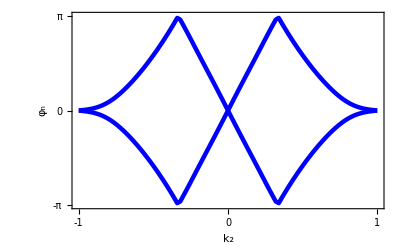

```mathematica
θo=Table[Sort[θ[[i,;;]]],{i,1,Dimensions[θ][[1]]}];
(*θo[[1]]={-1.,1.};*)
(*θo[[Dimensions[θ][[1]]]]={-1.,1.};*)
(*θo[[(Dimensions[θo][[1]]-1)/2+1]]={-1.,1.};*)
ListPlot[Table[θo[[1;;,i]],{i,1,BNbr}],Joined->True, PlotRange->{{-1.005,1.005},{-1.0,1.0}},Frame->True,FrameLabel->{"k_2","φ_n"},FrameTicks->{{{{-1,"-π"},0,{1,"π"}},None},{{-1,0,1},None}},DataRange->{-1,1},PlotStyle->{Directive[{Thickness[0.008],Blue}]},LabelStyle->{Directive[20],Black}]
```